```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework7

```mathematica
drand=ReadList["drand48.out"]
```

{0.396465,0.840485,0.353336,0.446583,0.318693,0.886428,0.015583,0.58409,0.159369,0.383716,0.691004,99978,0.917982,0.26955,0.142887,0.514615,0.432612,0.647449,0.258712,0.790128,0.168245,0.272164,0.380289}
 |  |  |  |

```mathematica
gaussrnd=ReadList["gaussrnd.out"]
```

{0.732369,-1.36197,1.14332,-2.49159,-1.42733,0.80165,0.237454,-1.87627,-0.871427,-1.25001,99980,-0.462216,2.35465,0.671176,0.90388,2.31771,-0.09378,-1.67948,0.128422,-0.184669,0.490384}
 |  |  |  |

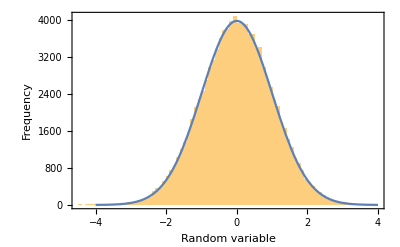

```mathematica
normaldist=Show[Histogram[gaussrnd,100],Plot[10000*PDF[NormalDistribution[],x],{x,-4,4}],Frame->True,FrameLabel->{"Random variable","Frequency","Distribution of gaussrnd() function"} ]
```

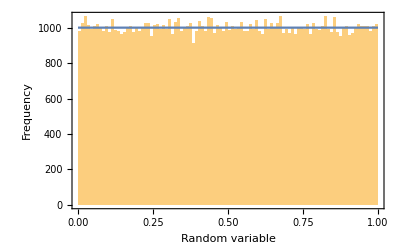

```mathematica
unidist=Show[Histogram[drand,100],Plot[1000*PDF[UniformDistribution[],x],{x,0,1}],Frame->True,FrameLabel->{"Random variable","Frequency","Distribution of drand48() function"} ]
```

```mathematica
Export["uniform_dist.png",unidist]
```

uniform_dist.png

```mathematica
Export["normal_dist.png",normaldist]
```

normal_dist.png

```mathematica
logdist=ReadList["logdist.out"]
```

{3.20205,3.35262,3.49034,3.3885,2.49135,2.21191,2.41018,2.70833,1.65343,3.44128,2.67745,99978,3.23165,3.02316,3.78792,2.94439,3.53129,3.78019,2.83422,3.10248,2.26722,2.76159,2.97855}
 |  |  |  |

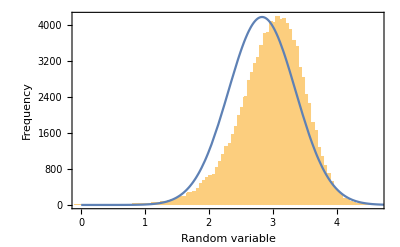

```mathematica
loghist=Show[Histogram[logdist,100],Plot[5500*PDF[NormalDistribution[Log[17],Sqrt[80/289]],x],{x,0,5}],Frame->True,FrameLabel->{"Random variable","Frequency","Distribution of log(x^2+y^2) function"} ]
```

```mathematica
Export["log_dist.png",loghist]
```

log_dist.png

```mathematica
gfits=ReadList["cannonball_gfits.log",Number]
```

{-9.42701,-9.35439,-9.45632,-9.40734,-9.36322,-9.41166,-9.35422,-9.43192,-9.31441,-9.36549,99980,-9.38424,-9.3833,-9.3384,-9.42724,-9.44225,-9.37363,-9.35217,-9.305,-9.37464,-9.35488}
 |  |  |  |

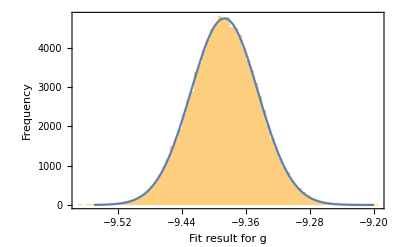

```mathematica
ghist=Show[Histogram[gfits,100],Plot[500*PDF[NormalDistribution[-9.387,0.042],x],{x,-9.55,-9.2}],Frame->True,FrameLabel->{"Fit result for g","Frequency","Distribution of χ^2 fits for g"}]
```

```mathematica
Mean[gfits]
```

-9.38692

```mathematica
StandardDeviation[gfits]
```

0.04199

```mathematica
Export["g_hist.png",ghist]
```

g_hist.png

```mathematica
cannon=ReadList["cannonball.dat",{Number,Number,Number}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

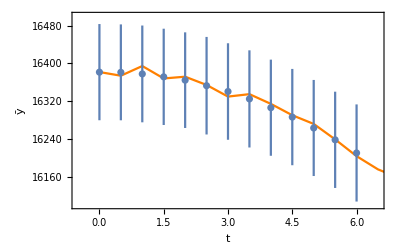

```mathematica
ytplot=Show[ListLinePlot[cannon[[;;,{1,2}]],PlotStyle->Orange],ErrorListPlot[{{{0,16381.324},ErrorBar[101.9032588569]},{{0.5,16380.892},ErrorBar[101.562983076]},{{1,16377.565},ErrorBar[102.517]},{{1.5,16371.346},ErrorBar[101.98314618]},{{2,16364.338},ErrorBar[101.2963756]},{{2.5,16352.602},ErrorBar[103.3304388]},{{3,16340.29},ErrorBar[102.216]},{{3.5,16324.632},ErrorBar[102.9111]},{{4,16306},ErrorBar[101.82102]},{{4.5,16286.142},ErrorBar[102.01161]},{{5,16263.033},ErrorBar[101.7557186]},{{5.5,16237.939},ErrorBar[101.9668]},{{6,16210.079},ErrorBar[102.881893]}}],PlotRange->{{-0.5,6.5},{16100,16500}},Frame->True, FrameLabel->{"t","ȳ", "Average values for y(t)"}]
```

```mathematica
Export["yt_plot.png",ytplot]
```

yt_plot.png

```mathematica
t2=ReadList["cannonball_g_montecarlo.log"]
```

{30.5261,-12.5912,2.57462,-39.2756,-29.1331,-26.6488,-5.39202,-0.583313,-19.6012,99982,-28.5131,-32.1267,-1.29458,36.0804,-34.4022,-23.7223,-13.6151,-6.08034,-30.1098}
 |  |  |  |

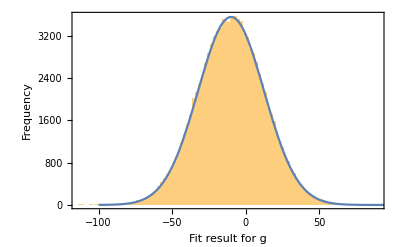

```mathematica
mchist=Show[Histogram[t2,100],Plot[200000*PDF[NormalDistribution[Mean[t2],StandardDeviation[t2]],x],{x,-100,100}],Frame->True,FrameLabel->{"Fit result for g","Frequency","Distribution of Monte Carlo fits for g"}]
```

```mathematica
Export["task2hist.png",mchist]
```

task2hist.png

```mathematica
t3=ReadList["cannonball_g_bootstrap.log",Number]
```

{6.45279,8.95346,-6.81645,-12.13,-37.6139,22.6807,-42.7882,3.58396,16.3958,35.1429,99980,13.5835,12.5372,-28.2171,-16.8184,-24.4315,-31.2495,-24.1171,29.2094,18.826,5.25192}
 |  |  |  |

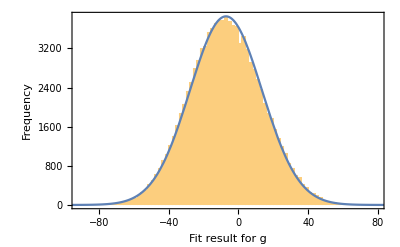

```mathematica
bootstraphist=Show[Histogram[t3,100],Plot[200000*PDF[NormalDistribution[Mean[t3],StandardDeviation[t3]],x],{x,-100,100}],Frame->True,FrameLabel->{"Fit result for g","Frequency","Distribution of bootstrapped fits for g"}]
```

```mathematica
Export["task3hist.png",bootstraphist]
```

task3hist.png

```mathematica
Mean[t2]
Mean[t3]
```

-9.92509

-7.16014

```mathematica
StandardDeviation[t2]
StandardDeviation[t3]
```

22.4278

20.6902